# Математическа статистика 2024-2025 учебна година доц. Петър Копанов

чертаене на хистограми и гладки хистограми на генерирани извадки 

	 за всяко от разпределенията се препоръчва да се сменят няколко стойности на размера на извадката n: 
	  n=10,100, 1000, 10000

## 1 чертаене на хистограма на Нормално разпределение Normal Distribution

Генерирана извадка:

Обем на извадката: 1000

Параметри и точкови оценки:

μ=0.       X̄=0.0429222

σ=1.       s=1.0085

Получени оценки на параметрите:

NormalDistribution[0.0429222,1.008]

Теоретично и емпирично средно:

E(X)=0.       X̄=0.0429222

Теоретична и емпирична дисперсия:

D(X) = 1.    S = 1.01707

хистограма на извадката:

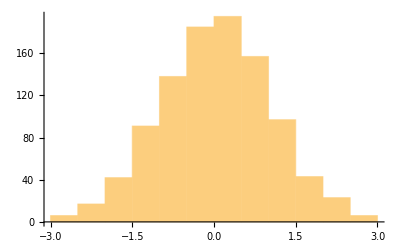

изгладена хистограма на извадката:

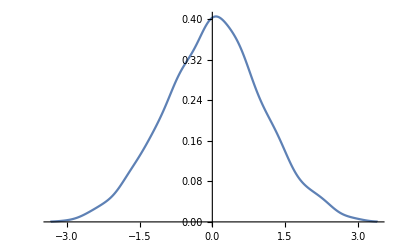

Хистограма, гладка хистограма и плътност на разпределението:

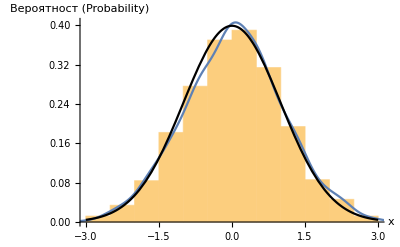

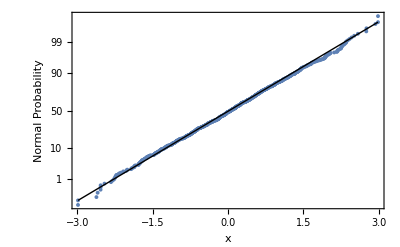

```mathematica
Clear["Global`*"]
Clear[data]
n=1000; (*   задаване обема на извадката *)
μ =0.; (*   задаване параметъра μ *)
σ = 1.0;(*   задаване параметъра σ *)
Print ["      Генерирана извадка:"]
data=RandomVariate[NormalDistribution[μ, σ],n];

Print ["  "]
Print ["      Обем на извадката: ", n]
Print ["      Параметри и точкови оценки: "]
Print ["  μ=", μ, "       X̄=", Mean[data]]
Print ["  σ=", σ, "       s=", StandardDeviation[data]]
Print ["   Получени оценки на параметрите:"]
EstimatedDistribution[data,NormalDistribution[μ0, σ0]]
Print ["  "]
Print ["      Теоретично и емпирично средно: "]
Print ["      E(X)=", Mean [NormalDistribution[μ, σ]], "       X̄=", Mean[data]]
Print ["      Теоретична и емпирична дисперсия: "]
Print ["      D(X) = ", Variance [NormalDistribution[μ, σ]], "    S = ", Variance[data]]
Print ["  "]
Print["                 хистограма на извадката: "]
Print ["  "]
Histogram[data]
Print ["  "]
Print ["  "]
Print["                изгладена хистограма на извадката: "]
Print ["  "]
SmoothHistogram[data]
Print ["  "]
Print ["  "]

Print ["         Хистограма, гладка хистограма и плътност на разпределението: "]
Show[Histogram[data,Automatic,"PDF",AxesLabel->{"x","Вероятност (Probability)"}], SmoothHistogram[data,Automatic],Plot[PDF[NormalDistribution[μ, σ],x],{x,μ-3*σ,μ+3*σ},PlotStyle->Black]]
ProbabilityScalePlot[data,"Normal",FrameLabel->{"x","Normal Probability"}]
```

## 2 чертаене на хистограма на експоненциално разпределение Exponential Distribution

Генерирана извадка:

Обем на извадката: 1000

Параметри и точкови оценки:

λ=0.3       0.288206

Получени оценки на параметрите:

ExponentialDistribution[0.288206]

Теоретично и емпирично средно:

E(X)=3.33333       X̄=3.46974

Теоретична и емпирична дисперсия:

D(X) = 11.1111    S = 12.5301

хистограма на извадката:

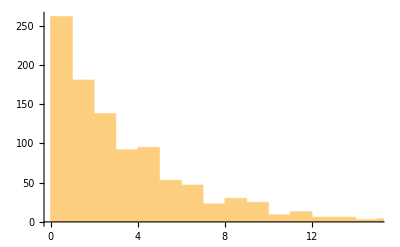

изгладена хистограма на извадката:

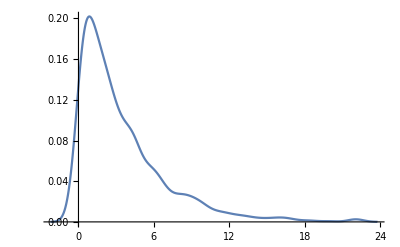

Хистограма, гладка хистограма и плътност на разпределението:

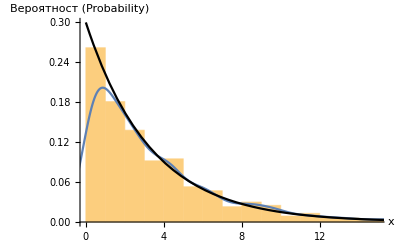

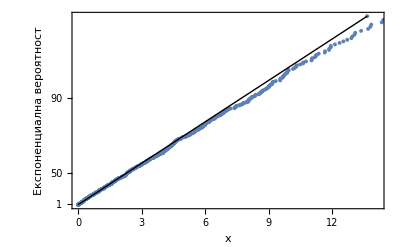

```mathematica
Clear["Global`*"]
Clear[data]
Print ["      Генерирана извадка:"]
n=1000; (*   задаване обема на извадката *)
λ=0.3; (*   задаване параметъра λ *)
data=RandomVariate[ExponentialDistribution[λ], n];

Print ["  "]
Print ["      Обем на извадката: ", n]
Print ["      Параметри и точкови оценки: "]
Print ["  λ=", λ, "       ", 1/Mean[data]]
Print ["   Получени оценки на параметрите:"]
EstimatedDistribution[data,ExponentialDistribution[λ0]]
Print ["  "]
Print ["      Теоретично и емпирично средно: "]
Print ["       E(X)=", Mean [ExponentialDistribution[λ]], "       X̄=", Mean[data]]
Print ["      Теоретична и емпирична дисперсия: "]
Print ["      D(X) = ", Variance [ExponentialDistribution[λ]], "    S = ", Variance[data]]
Print ["  "]
Print["                 хистограма на извадката: "]
Print ["  "]
Histogram[data]
Print ["  "]
Print ["  "]
Print["                изгладена хистограма на извадката: "]
Print ["  "]
SmoothHistogram[data]
Print ["  "]
Print ["  "]

Print ["         Хистограма, гладка хистограма и плътност на разпределението: "]
Show[Histogram[data,Automatic,"PDF",AxesLabel->{"x","Вероятност (Probability)"}], SmoothHistogram[data,Automatic],Plot[PDF[ExponentialDistribution[λ],x],{x,0,6/λ},PlotStyle->Black]]
ProbabilityScalePlot[data,"Exponential",FrameLabel->{"x","Експоненциална вероятност"}]
```

## 3 чертаене на хистограма на Равномерно разпределение Uniform Distribution

Генерирана извадка:

Обем на извадката: 1000

Параметри и точкови оценки:

a=1.       1.00124

b=3.       2.99965

Получени оценки на параметрите:

UniformDistribution[{1.00124,2.99965}]

Теоретично и емпирично средно:

E(X)=2.       X̄=2.01697

Теоретична и емпирична дисперсия:

D(X) = 0.333333    S = 0.331184

хистограма на извадката:

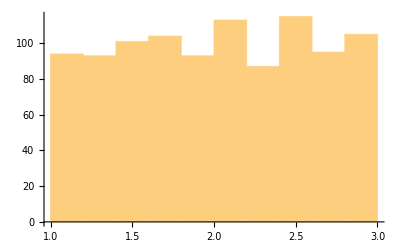

изгладена хистограма на извадката:

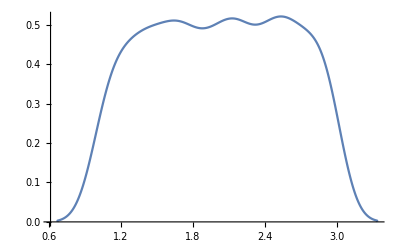

Хистограма, гладка хистограма и плътност на разпределението:

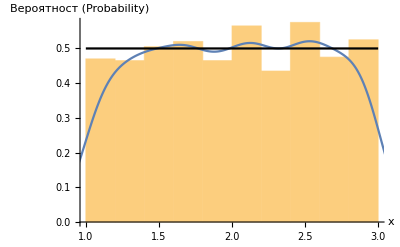

```mathematica
Clear["Global`*"]
Clear[data, a, b]
n=1000; (*   задаване обема на извадката *)
a=1.; (*   задаване параметъра a *)
b=3.; (*   задаване параметъра b *)

Print ["      Генерирана извадка:"]
data=RandomVariate[UniformDistribution[{a, b}], n];

Print ["  "]
Print ["      Обем на извадката: ", n]
Print ["      Параметри и точкови оценки: "]
Print ["  a=", a, "       ", Min[data]]
Print ["  b=", b, "       ", Max[data]]
Print ["   Получени оценки на параметрите:"]
EstimatedDistribution[data,UniformDistribution[{a0, b0}]]
Print ["  "]
Print ["      Теоретично и емпирично средно: "]
Print ["       E(X)=", Mean [UniformDistribution[{a, b}]], "       X̄=", Mean[data]]
Print ["      Теоретична и емпирична дисперсия: "]
Print ["       D(X) = ", Variance [UniformDistribution[{a, b}]], "    S = ", Variance[data]]
Print ["  "]
Print["                 хистограма на извадката: "]
Print ["  "]
Histogram[data]
Print ["  "]
Print ["  "]
Print["                изгладена хистограма на извадката: "]
Print ["  "]
SmoothHistogram[data]
Print ["  "]
Print ["  "]

Print ["         Хистограма, гладка хистограма и плътност на разпределението: "]
Show[Histogram[data,Automatic,"PDF",AxesLabel->{"x","Вероятност (Probability)"}], SmoothHistogram[data,Automatic],Plot[PDF[UniformDistribution[{a, b}],x],{x,a,b},PlotStyle->Black]]
(*ProbabilityScalePlot[data,"Uniform",FrameLabel->{"x","Равномерна вероятност"}]*)
```

## 4 чертаене на хистограма на разпределение на Коши Cauchy Distribution

Генерирана извадка:

Обем на извадката: 1000

Параметри и точкови оценки:

a=0       1.54223

Получени оценки на параметрите:

CauchyDistribution[0.342722,3.08554]

хистограма на извадката:

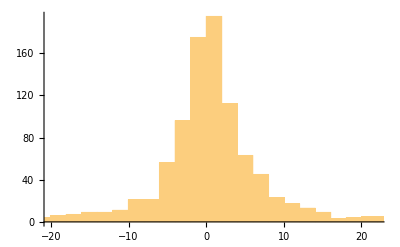

изгладена хистограма на извадката:

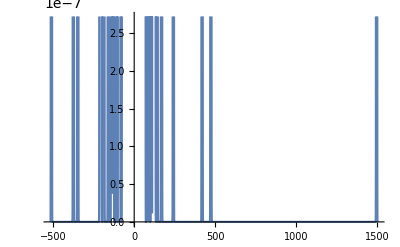

Хистограма, гладка хистограма и плътност на разпределението:

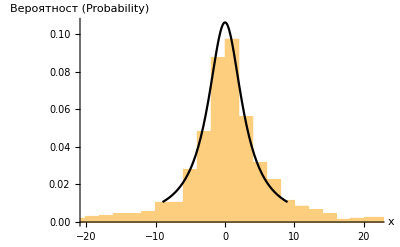

```mathematica
Clear["Global`*"]
Clear[data, a, b]
n=1000; (*   задаване обема на извадката *)
a=0; (*   задаване параметъра a *)
b=3;(*   задаване параметъра b *)
Print ["      Генерирана извадка:"]
data=RandomVariate[CauchyDistribution[a, b],n];

Print ["  "]
Print ["      Обем на извадката: ", n]
Print ["      Параметри и точкови оценки: "]
Print ["  a=", a, "       ", Mean[data]]
Print ["   Получени оценки на параметрите:"]
EstimatedDistribution[data,CauchyDistribution[a0, b0]]
Print ["  "]
Print["                 хистограма на извадката: "]
Print ["  "]
Histogram[data]
Print ["  "]
Print ["  "]
Print["                изгладена хистограма на извадката: "]
Print ["  "]
SmoothHistogram[data]
Print ["  "]
Print ["  "]

Print ["         Хистограма, гладка хистограма и плътност на разпределението: "]
Show[Histogram[data,Automatic,"PDF",AxesLabel->{"x","Вероятност (Probability)"}], SmoothHistogram[data,Automatic],Plot[PDF[CauchyDistribution[a, b],x],{x,a-3 b,a+3 b},PlotStyle->Black]]
(*ProbabilityScalePlot[data,"Cauchy",FrameLabel->{"x"," Вероятност на Коши "}] *)
```

## 5 чертаене на хистограма на разпределение на Рейли Rayleigh distribution

Генерирана извадка:

Обем на извадката: 3000

Параметри и точкови оценки:

σ=7.       7.02492

Получени оценки на параметрите:

RayleighDistribution[6.99242]

Теоретично и емпирично средно:

E(X)=8.7732       X̄=8.80443

Теоретична и емпирична дисперсия:

D(X) = 21.031    S = 20.2766

хистограма на извадката:

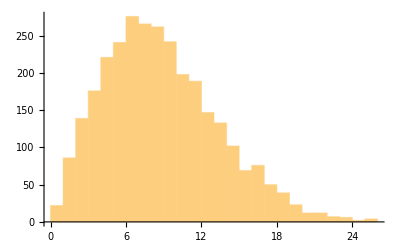

изгладена хистограма на извадката:

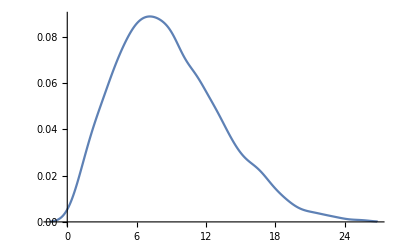

Хистограма, гладка хистограма и плътност на разпределението:

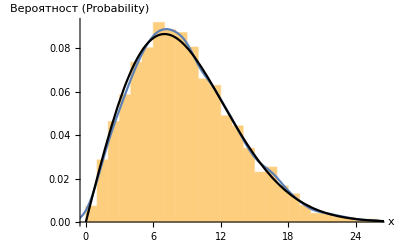

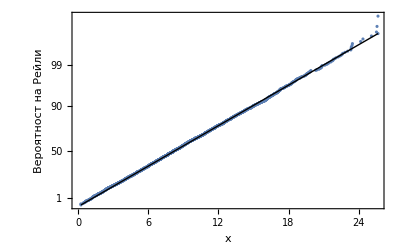

```mathematica
Clear["Global`*"]
Clear[data]
n=3000; (*   задаване обема на извадката *)
σ = 7.; (*   задаване параметъра σ *)
Print ["      Генерирана извадка:"]
data=RandomVariate[RayleighDistribution[σ],n];

Print ["  "]
Print ["      Обем на извадката: ", n]
Print ["      Параметри и точкови оценки: "]
Print ["  σ=", σ, "       ", Mean[data]*√(2/π)]
Print ["   Получени оценки на параметрите:"]
EstimatedDistribution[data,RayleighDistribution[σ0]]
Print ["  "]
Print ["      Теоретично и емпирично средно: "]
Print ["       E(X)=", Mean [RayleighDistribution[σ]], "       X̄=", Mean[data]]
Print ["      Теоретична и емпирична дисперсия: "]
Print ["       D(X) = ", Variance [RayleighDistribution[σ]], "    S = ", Variance[data]]
Print ["  "]
Print["                 хистограма на извадката: "]
Print ["  "]
Histogram[data]
Print ["  "]
Print ["  "]
Print["                изгладена хистограма на извадката: "]
Print ["  "]
SmoothHistogram[data]
Print ["  "]
Print ["  "]

Print ["         Хистограма, гладка хистограма и плътност на разпределението: "]
Show[Histogram[data,Automatic,"PDF",AxesLabel->{"x","Вероятност (Probability)"}], SmoothHistogram[data,Automatic],Plot[PDF[RayleighDistribution[σ],x],{x,0,4*σ},PlotStyle->Black]]
ProbabilityScalePlot[data,"Rayleigh",FrameLabel->{"x","Вероятност на Рейли"}]
```

## 6 чертаене на хистограма на разпределение на Стюдънт Student T Distribution

Генерирана извадка:

Обем на извадката: 5000

Параметри и точкови оценки:

n=7       6.51931

Получени оценки на параметрите:

StudentTDistribution[6.74024]

Теоретично и емпирично средно:

E(X)=0       X̄=0.00867559

Теоретична и емпирична дисперсия:

D(X) = 7/5    S = 1.44255

хистограма на извадката:

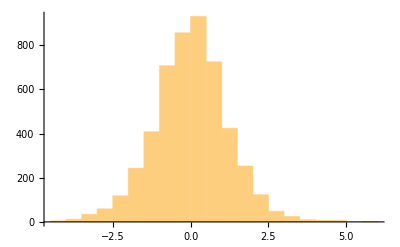

изгладена хистограма на извадката:

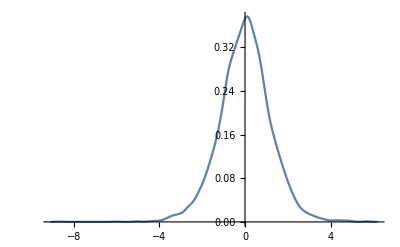

Хистограма, гладка хистограма и плътност на разпределението:

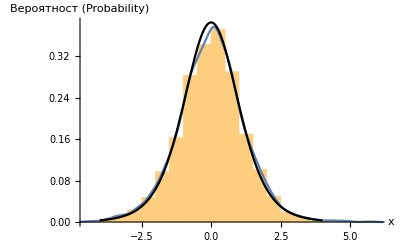

```mathematica
Clear["Global`*"]
n=5000; (*   задаване обема на извадката *)
nn = 7; (*   задаване параметъра n *)
Print ["      Генерирана извадка:"]
data=RandomVariate[StudentTDistribution[nn],n];

Print ["  "]
Print ["      Обем на извадката: ", n]

Print ["  "]
Print ["      Параметри и точкови оценки: "]
Print ["  n=", nn, "       ", 2*Variance[data]/(Variance[data]-1)]
Print ["   Получени оценки на параметрите:"]
EstimatedDistribution[data,StudentTDistribution[nn0]]
Print ["      Теоретично и емпирично средно: "]
Print ["      E(X)=", Mean [StudentTDistribution[nn]], "       X̄=", Mean[data]]
Print ["      Теоретична и емпирична дисперсия: "]
Print ["      D(X) = ", Variance [StudentTDistribution[nn]], "    S = ", Variance[data]]
Print ["  "]
Print["                 хистограма на извадката: "]
Print ["  "]
Histogram[data]
Print ["  "]
Print ["  "]
Print["                изгладена хистограма на извадката: "]
Print ["  "]
SmoothHistogram[data]
Print ["  "]
Print ["  "]

Print ["         Хистограма, гладка хистограма и плътност на разпределението: "]
Show[Histogram[data,Automatic,"PDF",AxesLabel->{"x","Вероятност (Probability)"}], SmoothHistogram[data,Automatic],Plot[PDF[StudentTDistribution[nn],x],{x,-4,4},PlotStyle->Black]]
(*ProbabilityScalePlot[data,"Student",FrameLabel->{"x","Вероятност на Стюдънт"}] *)
```

## 7 чертаене на хистограма на Г-разпределение GammaDistribution

Генерирана извадка:

Обем на извадката: 10000

Параметри и точкови оценки:

α=1.5       1.49859

β=3.       3.02454

Получени оценки на параметрите:

GammaDistribution[1.52583,2.97054]

Теоретично и емпирично средно:

E(X)=4.5       X̄=4.53254

Теоретична и емпирична дисперсия:

D(X) = 13.5    S = 13.7088

хистограма на извадката:

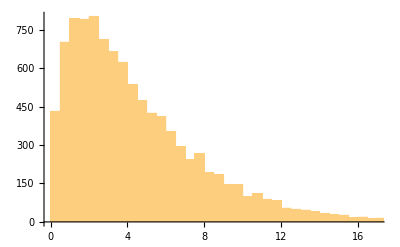

изгладена хистограма на извадката:

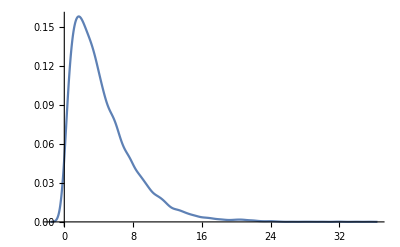

Хистограма, гладка хистограма и плътност на разпределението:

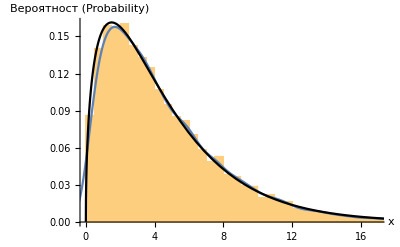

```mathematica
Clear["Global`*"]
n=10000; (*   задаване обема на извадката *)
α =1.5; (*   задаване параметъра α *)
β = 3.0;(*   задаване параметъра β *)
Print ["      Генерирана извадка:"]
data=RandomVariate[GammaDistribution[α,β],n];

Print ["  "]
Print ["      Обем на извадката: ", n]
Print ["      Параметри и точкови оценки: "]
Print ["  α=", α, "       ", Mean[data]^2/Variance[data]]
Print ["  β=", β, "       ", Variance[data]/Mean[data]]
Print ["   Получени оценки на параметрите:"]
EstimatedDistribution[data,GammaDistribution[α0,β0]]
Print ["  "]
Print ["      Теоретично и емпирично средно: "]
Print ["      E(X)=", Mean [GammaDistribution[α,β]], "       X̄=", Mean[data]]
Print ["      Теоретична и емпирична дисперсия: "]
Print ["      D(X) = ", Variance [GammaDistribution[α,β]], "    S = ", Variance[data]]
Print ["  "]
Print["                 хистограма на извадката: "]
Print ["  "]
Histogram[data]
Print ["  "]
Print ["  "]
Print["                изгладена хистограма на извадката: "]
Print ["  "]
SmoothHistogram[data]
Print ["  "]
Print ["  "]

Print ["         Хистограма, гладка хистограма и плътност на разпределението: "]
Show[Histogram[data,Automatic,"PDF",AxesLabel->{"x","Вероятност (Probability)"}], SmoothHistogram[data,Automatic],Plot[PDF[GammaDistribution[α,β],x],{x,0, 5*α*β},PlotStyle->Black]]
(*ProbabilityScalePlot[data,"Gamma",FrameLabel->{"x","Normal Probability"}]*)
```

## Задача 8.

```mathematica
Clear["Global`*"]
```

## Задача 9.

```mathematica
Clear["Global`*"]
```

## Задача 10.

```mathematica
Clear["Global`*"]
```

## Задача 11.

```mathematica
Clear["Global`*"]
```

## Задача 12.

```mathematica
Clear["Global`*"]
```

## Задача 13.

```mathematica
Clear["Global`*"]
```

## Задача 14.

```mathematica
Clear["Global`*"]
```

## Задача 15.

```mathematica
Clear["Global`*"]
```

## Задача 16.

```mathematica
Clear["Global`*"]
```

## Задача 17.

```mathematica
Clear["Global`*"]
```

## Задача 18.

```mathematica
Clear["Global`*"]
```

## Задача 19.

```mathematica
Clear["Global`*"]
```

## Задача 20.

```mathematica
Clear["Global`*"]
```

## Задача 21.

```mathematica
Clear["Global`*"]
```

## Задача 22.

```mathematica
Clear["Global`*"]
```

## Задача 23.

```mathematica
Clear["Global`*"]
```

## Задача 24.

```mathematica
Clear["Global`*"]
```

## Задача 25.

```mathematica
Clear["Global`*"]
```

## Задача 26.

```mathematica
Clear["Global`*"]
```

## Задача 27.

```mathematica
Clear["Global`*"]
```

## Задача 28.

```mathematica
Clear["Global`*"]
```

## Задача 29.

```mathematica
Clear["Global`*"]
```

## Задача 30.По-долу за илюстрация сме дали няколко скали на разпределение за равномерни данни

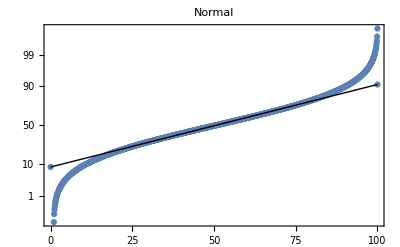
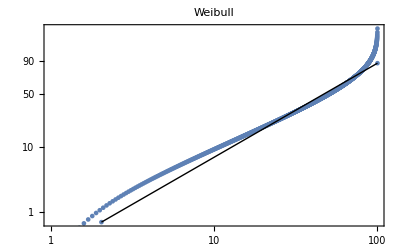
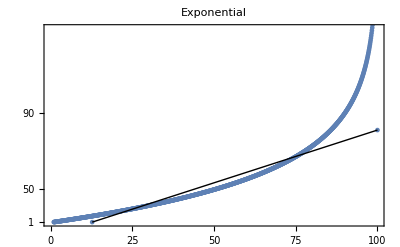
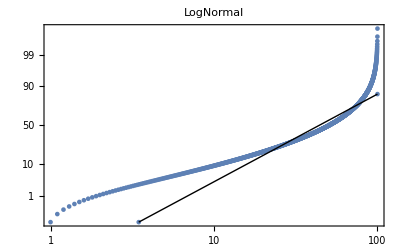
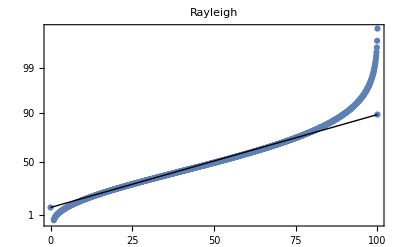
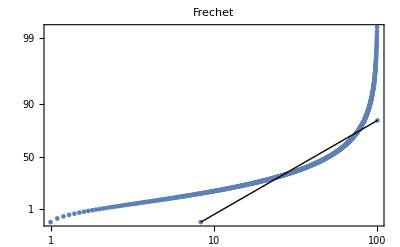
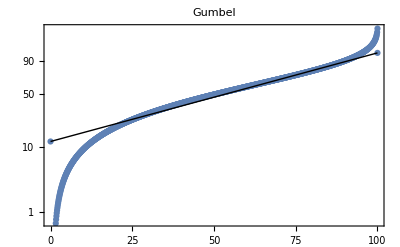

```mathematica
Clear["Global`*"]
Table[ProbabilityScalePlot[Range[1,100,0.1],ref,PlotLabel->ref],{ref,{"Normal", "Weibull","Exponential","LogNormal","Rayleigh","Frechet", "Gumbel"}}]
```